```mathematica
vradius =.4;
hradius = .5;
f[x_, y_] := Piecewise[
{
{Sqrt[Abs[vradius^2(1 - (1/hradius^2 )y^2)]*(1 - 1/(hradius-y)^2 x^2)], 
y >= 0 && y < hradius},
{Sqrt[Abs[vradius^2(1 - (1/hradius^2 )y^2)]*(1 - 1/(hradius - -y)^2x^2)], 
y < 0 && y > -hradius},
{0, y < -hradius || y > hradius}
}
]
f[0, .5]
t = Plot3D[f[x,y], {x, -hradius,hradius},{y,-hradius,hradius},Exclusions->None, AxesLabel->{x,y, z},PlotStyle->Blue];
b =  Plot3D[-f[x,y], {x, -hradius,hradius},{y,-hradius,hradius}, Exclusions->None,AxesLabel->{x,y, z},  PlotStyle->Blue];


Show[t, b, PlotRange->{{-hradius,hradius},{-hradius,hradius}, {-hradius,hradius}},ImageSize->Scaled[1]]
```

0

-Graphics3D-

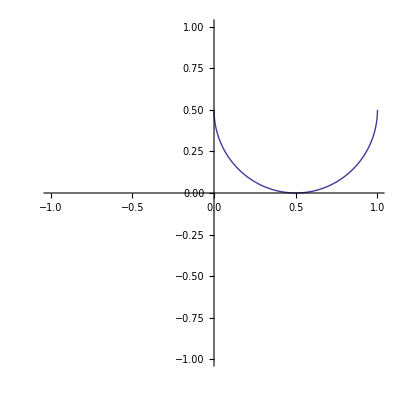

```mathematica
Plot[hradius + -Sqrt[hradius^2 - (x - hradius)^2], {x, -1, 1}, PlotRange->{-1, 1}, AspectRatio->1]
```